# Readout/initialisation on Delft’s Silicon device

reference: https://arxiv.org/abs/2202.09252

Set environment, such as threads, gpu, etc.

```mathematica
SetEnvironment["OMP_NUM_THREADS"->"8"]
SetDirectory[NotebookDirectory[]];
```

Load the QuESTLink

```mathematica
Import["/home/cica/programs/QuESTlink/Link/QuESTlink.m"];
CreateLocalQuESTEnv["../../quest_link_cpu"];
```

Connectivity of this device

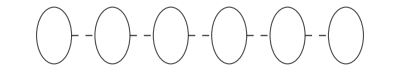

```mathematica
nodes=Labeled[#,Placed[{#,"Q"<>ToString[#+1]},{Below,Center}]]&/@Range[0,5];
Graph[nodes,Table[j<->j+1,{j,nodes[[All,1]][[;;-2]]}],VertexSize->0.6,VertexStyle->Directive[White,EdgeForm[Thick]],BaseStyle->{11,FontFamily->"Serif"},ImageSize->Automatic,EdgeStyle->Directive[Black,Thick,Dashed]]
```

## Readout test: parity measurement

```mathematica
ReadP::usage="Parity readout/measurement between 2 qubits, 1=even, 0=odds. The readout uses an ancilla in the hidden qubit to do projective measurement on the parity measurement.
P=ZZ; P_(+1)=II+ZZ, P_-1=II-ZZ";
```

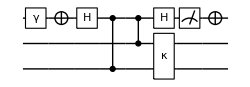
Note that, direct readouts are only possible via parity measurements, where it can only be done on the edge qubits, 
where the even parity outputs “1” and odds parity outputs “0”. This can be simulated with the following circuits:

  =   -Graphics-

```mathematica
Subscript[tdecay, q0_,q1_]:=Subscript[Kraus, q0,q1][
{{{1,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},
{{0,0,0,0},{0,0,1,0},{0,0,0,0},{0,0,0,0}},
{{0,0,0,0},{0,1,0,0},{0,0,0,0},{0,0,0,0}},
{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,1}}}
]
```

```mathematica
Subscript[ReadP, q0_,q1_][a_]:={Subscript[Damp, a][1],Subscript[X, a],Subscript[H, a],Subscript[C, a][Subscript[Z, q0]],Subscript[C, a][Subscript[Z, q1]],Subscript[H, a],Subscript[M, a],Subscript[tdecay, q0,q1]}
```

```mathematica
ρ=CreateDensityQureg[3];
```

```mathematica
Flatten[Table[
InitZeroState@ρ;
(*set the initial state *)
If[q0==1,ApplyCircuit[ρ,Subscript[X, 0]]];
If[q1==1,ApplyCircuit[ρ,Subscript[X, 1]]];
out=ApplyCircuit[ρ,Subscript[ReadP, 0,1][2]];
{q0,q1,out,Sequence@@Flatten@ApplyCircuit[ρ,{Subscript[M, 0],Subscript[M, 1]}]}
,{q0,0,1},{q1,0,1}],1];
TableForm[%,TableHeadings->{None,{"ψ_init","outcome","ψfinal"}},TableAlignments->Center]
```

ψ_init | outcome | ψfinal
0,0 | 1 | 0,0
0,1 | 0 | 1,0
1,0 | 0 | 1,0
1,1 | 1 | 1,1

## The real-time feedback initialisation on edge qubits: 0,1 and 5,4

```mathematica
meas01=Flatten@{Subscript[ReadP, 0,1],Subscript[C, 0][Subscript[X, 0]],Subscript[ReadP, 0,1][2]}
```

{ReadP_(0,1),C_0[X_0],Damp_2[1],X_2,H_2,C_2[Z_0],C_2[Z_1],H_2,M_2,Kraus_(0,1)[{{{1,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,1,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,1,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,1}}}]}

```mathematica
Subscript[ReadInit, q0_,q1_][ρ_,ancilla_]:=Module[{m0,m1},
m0=First@Flatten@ApplyCircuit[ρ,Subscript[ReadP, q0,q1][ancilla]];
(*If even parity *)
If[m0==1,ApplyCircuit[ρ,Subscript[X, q0]]];
m1=First@Flatten@ApplyCircuit[ρ,Subscript[ReadP, q0,q1][ancilla]];
{m0,m1}
]
```

```mathematica
Flatten[Table[
InitZeroState@ρ;
(*set the initial state *)
If[q0==1,ApplyCircuit[ρ,Subscript[X, 0]]];
If[q1==1,ApplyCircuit[ρ,Subscript[X, 1]]];
{m0,m1}=Subscript[ReadInit, 0,1][ρ,2];
{q0,q1,StringRiffle[{m0,m1},""],Sequence@@Flatten@ApplyCircuit[ρ,{Subscript[M, 0],Subscript[M, 1]}]}
,{q0,0,1},{q1,0,1}],1];
TableForm[%,TableHeadings->{None,{"ψ_init","outcomes","ψfinal"}},TableAlignments->Center]
```

ψ_init | outcomes | ψfinal
0,0 | 10 | 1,0
0,1 | 00 | 1,0
1,0 | 00 | 1,0
1,1 | 10 | 1,0

## QND on qubit3: state3 doesn’t change but others yes

```mathematica
ρ4=CreateDensityQureg[4];
```

```mathematica
Flatten[Table[
InitZeroState@ρ4;
(*set the initial state *)
If[q0==1,ApplyCircuit[ρ4,Subscript[X, 0]]];If[q1==1,ApplyCircuit[ρ4,Subscript[X, 1]]];If[q2==1,ApplyCircuit[ρ4,Subscript[X, 2]]];
(* read edges*)
{m0,m1}=Subscript[ReadInit, 0,1][ρ4,3];
ApplyCircuit[ρ4,Subscript[C, 2][Subscript[X, 1]]];
(*Final state*)
m2=First@Flatten@ApplyCircuit[ρ4,Subscript[ReadP, 0,1][3]];
mfin=Flatten@ApplyCircuit[ρ4,{Subscript[M, 0],Subscript[M, 1],Subscript[M, 2]}];
{q0,q1,q2,StringRiffle[{m0,m1,m2},""],Sequence@@mfin}
,{q0,0,1},{q1,0,1},{q2,0,1}],2];
TableForm[%,TableHeadings->{None,{"ψ_init","outcomes","ψfinal"}},TableAlignments->Center]
```

ψ_init | outcomes | ψfinal
0,0,0 | 100 | 1,0,0
0,0,1 | 101 | 1,1,1
0,1,0 | 000 | 1,0,0
0,1,1 | 001 | 1,1,1
1,0,0 | 000 | 1,0,0
1,0,1 | 001 | 1,1,1
1,1,0 | 100 | 1,0,0
1,1,1 | 101 | 1,1,1

Read4: needs swap

```mathematica
ρ5=CreateDensityQureg[5];
```

```mathematica
Flatten[Table[
InitZeroState@ρ5;
(*set the initial state *)
If[q0==1,ApplyCircuit[ρ5,Subscript[X, 0]]];If[q1==1,ApplyCircuit[ρ5,Subscript[X, 1]]];If[q2==1,ApplyCircuit[ρ5,Subscript[X, 2]]];If[q3==1,ApplyCircuit[ρ5,Subscript[X, 3]]];
(* read edges*)
{m0,m1}=Subscript[ReadInit, 0,1][ρ5,4];
ApplyCircuit[ρ5,{Subscript[C, 3][Subscript[X, 1]]}];
(*Final state*)
m2=First@Flatten@ApplyCircuit[ρ5,Subscript[ReadP, 0,1][4]];
mfin=Flatten@ApplyCircuit[ρ5,{Subscript[M, 0],Subscript[M, 1],Subscript[M, 2],Subscript[M, 3]}];
{q0,q1,q2,q3 ,StringRiffle[{m0,m1,m2},""],Sequence@@mfin}
,{q0,0,1},{q1,0,1},{q2,0,1},{q3,0,1}],3];
TableForm[%,TableHeadings->{None,{"ψ_init","outcomes","ψfinal"}},TableAlignments->Center]
```

ψ_init | outcomes | ψfinal
0,0,0,0 | 100 | 1,0,0,0
0,0,0,1 | 101 | 1,1,0,1
0,0,1,0 | 100 | 1,0,1,0
0,0,1,1 | 101 | 1,1,1,1
0,1,0,0 | 000 | 1,0,0,0
0,1,0,1 | 001 | 1,1,0,1
0,1,1,0 | 000 | 1,0,1,0
0,1,1,1 | 001 | 1,1,1,1
1,0,0,0 | 000 | 1,0,0,0
1,0,0,1 | 001 | 1,1,0,1
1,0,1,0 | 000 | 1,0,1,0
1,0,1,1 | 001 | 1,1,1,1
1,1,0,0 | 100 | 1,0,0,0
1,1,0,1 | 101 | 1,1,0,1
1,1,1,0 | 100 | 1,0,1,0
1,1,1,1 | 101 | 1,1,1,1